# Homotopy Pics

The plan is to make some pics to understand the behavior of the homotopy curves.

```mathematica
p2[{z1_,z2_}]:= {3I + (1+I)z1 z2 + z1^3-1,1+I z2^3-z2^2 z1^2+ 3 z1 z2+z1};
p2Zero[{z1_,z2_}]:= {z1^3-1,1+I z2^3-z2^2 z1^2};
rootSubZero=NSolve[p2Zero[{z1,z2}]=={0,0},{z1,z2}] ;
rootSub=NSolve[p2[{z1,z2}]=={0,0},{z1,z2}] ;
{m,mZero}=Map[Length,{rootSub,rootSubZero}];

z1S=Table[{Hue[i/m],Point[ReIm[z1/.rootSub⟦i⟧]]},{i,m}];
z2S=Table[{Hue[i/m],Point[ReIm[z2/.rootSub⟦i⟧]]},{i,m}];
z1z2S=Table[{ Hue[i/m],Arrow[{ReIm[z1],ReIm[z2]}]/.rootSub⟦i⟧},{i,m}];
z1z2Start=Table[{ RandomColor[],Arrow[{ReIm[z1],ReIm[z2]}]/.rootSubZero⟦i⟧},{i,m}];
TabView[{
"z1"->Graphics[z1S,Frame->True,GridLines->Automatic],
"z2"->Graphics[z2S,Frame->True,GridLines->Automatic],
"z1z2S"->Graphics[{z1S,z2S,z1z2S},Frame->True,GridLines->Automatic],
"z1z2Start"->Graphics[{z1S,z2S,z1z2Start},Frame->True,GridLines->Automatic]
},3]
```

1234

I want to set up and solve the homotopy
	(1-t) p2Zero+t p2 ==0
The ODE is 
	(1-t)∂

```mathematica
Clear[p,z,t]
p[z_,t_]:= (1-t)p2Zero[z]+t p2[z]
A[{z1_,z2_},t_]= D[ p[{z1,z2},t],{{z1,z2}}];
AInv[{z1_,z2_},t_]= Inverse[D[ p[{z1,z2},t],{{z1,z2}}]];
b[{z1_,z2_},t_]=-D[ p[{z1,z2},t],t];
i=1;
z0={z1,z2}/.rootSubZero⟦i⟧;
AInv[z0,0].b[z0,0]
zSol=NDSolveValue[{z'[t]==AInv[z[t],t].b[z[t],t],z[0]==z0},z,{t,0,1}];
Manipulate[Graphics[{
{Dashed,z1z2S},
{Dotted,z1z2Start},
{Arrow[ReIm[zSol[t]]]}
}],{t,0, 1,0.01}]
```

{-1.06872+0.83248 ⅈ,-0.595294-0.203909 ⅈ}

```mathematica
Table[p[zA[t],t],{t, {0.0,0.1,0.2,0.3}}]
```

{{-3.04887-5.28979 ⅈ,-9.43124+2.21337 ⅈ},{-3.04887-5.28979 ⅈ,-9.43125+2.21337 ⅈ},{-3.04887-5.28979 ⅈ,-9.43125+2.21337 ⅈ},{-3.04887-5.28979 ⅈ,-9.43125+2.21337 ⅈ}}

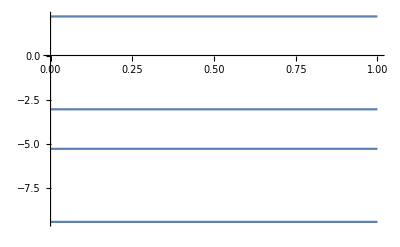

```mathematica
Plot[ ReIm[p[zA[t],t]],{t,0,1}]
```

```mathematica
ReIm[yA[0.9]]
```

{{1.79742,-1.50813},{1.56398,0.937756}}

```mathematica
AInv[
```

```mathematica
{m,mZero}
```

{9,9}